Projecting Data

Berechnung Maximaldruckkurve...

Clustering Training-portion

max windows now...

Durchschnitt des Ruhedrucks: 16.6006

Making Plots

-60

-Graphics-

-Graphics-

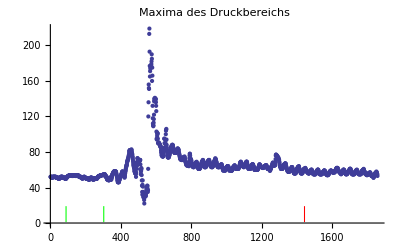

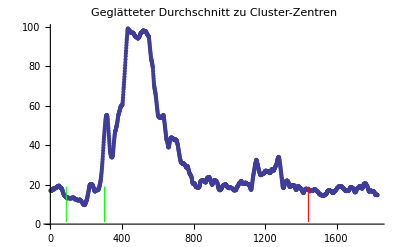

c:/work/drucksensoren-11.png

c:/work/fft-11.png

c:/work/maxima-11.png

c:/work/smooth-11.png

```mathematica
ClearAll[ComputeCentroids,data,dataWOIndex,dataDruck,dataWOIndex,cl2,numClusters,startIdx,endIdx,MinDist,endIdxRawString,centers,meanTrainingSet,startTraining,endTraining,schluckEndeStartPos,ruhedruck,ruhedruck2,ReadMarkers,markers,schluck,daten,datenFFT,bild1,bild2,bild3,bild4,directory,endeFFTRow,endeFFTRowLength,FindIndex,MaxIdx,MinIdx,dataTrain,centroidList,distances,startSearch,maxPlot,smoothPlot,marker,markerTrainLeft,markerTrainRight];

schluck="11";
directory="M:\\Proband2\\00511910Schluck"<>schluck<>".ASC.data";
dataDruck=(Import[directory<>"\\data.csv","Data","HeaderLines"->0]);
data=(Import[directory<>"\\result.csv","Data","HeaderLines"->0]);

$Distance=ManhattanDistance;

endeFFTRow=((Length[data[[1,All]]]+1)/2)-1;
endeFFTRowLength=endeFFTRow;
endeFFTRow=32;
data=data[[All,1;;endeFFTRow]];
dataWOIndex=data[[All,2;;endeFFTRow]];

numClusters=2;
startIdx=ToExpression[StringTake[(Import[directory<>"\\channelstart","Data","HeaderLines"->0]),{2}][[1]]]+1;
endIdxRawString = Import[StringJoin[directory, "\\channelend"], "Data", "HeaderLines" -> 0][[1]];
endIdx = ToExpression[StringTake[ToString[endIdxRawString], {2, Length[Characters[ToString[endIdxRawString]]]}]]+1;

ReadMarkers[base_]:=(

start1=Import[base<>"\\rdstart","Data","HeaderLines"->0][[1]];
ende1=Import[base<>"\\rdend","Data","HeaderLines"->0][[1]];
samplerate1=Import[base<>"\\samplerate","Data","HeaderLines"->0][[1]];
start2=StringSplit[start1,":"];
start3=ToExpression[start2[[2]]]+ToExpression[start2[[1]]]*60;
ende2=StringSplit[ende1,":"];
ende3=ToExpression[ende2[[2]]]+ToExpression[ende2[[1]]]*60;
Return[{start3*ToExpression[samplerate1],ende3*ToExpression[samplerate1]}];

);

markers=ReadMarkers[directory];
startTraining=markers[[1]]-data[[1,1]];
startTraining=Max[startTraining-endeFFTRowLength,1];
startTraining=startTraining+0;
endTraining=markers[[2]]-data[[1,1]];
endTraining=endTraining+0;

ComputeCentroids[clusteringComponents_,data_,numClusters_]:=(
centers=Reap[
For[i=1,i≤numClusters,i++,(
Clear[centroid,cnt];
centroid=Table[0,{i,endeFFTRow-1}];

cnt=0;
For[j=1,j≤Length[data],j++,(
If[clusteringComponents[[j]]==i,(

centroid+=data[[j]];
cnt++;
)];
)]; (*of For - data*)
centroid/=cnt;
Sow[centroid,sowcentroid]
(*Print["Centroid for cluster ",i,  " is ", centroid];
Print["Sample distance: ", ToString[EuclideanDistance[data[[1]],centroid]//N]];*)

)];

,sowcentroid];
Return[Flatten[centers[[2]],1]];
);

MinDist[list_,data_]:=(
ret=100000000000000;
For[j=1,j≤Length[list],j++,(
Clear[dist];
dist=$Distance[list[[j]],data];
ret=Min[ret,dist];
)];
(*Print[ret];*)
Return[ret];
);


FindIndex[distancesList_,startSeekIndex_,valueToFind_]:=(
l=Length[distancesList];
(*Print[distancesList]*);
idx=startSeekIndex;
(*Print["Start seeking for value ",ToString[valueToFind]," from Index ",ToString[startSeekIndex]];*)
While[idx≤l,(
If[distancesList[[idx]]≤valueToFind,Return[idx]];
idx++;
)];
Return[Length[distancesList]];
);
MaxIdx[list_]:=(
m=Max[list];
For[j=1,j≤Length[list],j++,(
If[list[[j]]==m,(
Return[j]
)];
)];
);
MinIdx[list_,idx_]:=(
t=idx;
c=list[[t]];
p=list[[t+1]];
d=+1;
If[p<c,d=1,d=-1];
While[list[[t+d]]<list[[t]],t=t+d];
Return[t];

);

Print["Projecting Data"];
dataTrain=dataWOIndex[[startTraining;;(endTraining-endeFFTRow),All]];

(*
Berechnet das jeweilige Max des Sensor-bereichs über die gesamten Daten.
Ziel ist die Identifizierung des Max-Drucks in dem gesamten Bereich, von dem aus 
die Suche des Ruhedrucks starten wird.
*)

Print["Berechnung Maximaldruckkurve..."];
maxWindow=ParallelTable[Max[dataDruck[[i,startIdx;;endIdx]]],{i,1,Length[dataDruck[[All,1]]]}];
(*normWindow=ParallelTable[Norm[data[[i,2;;48]]],{i,0,Length[data[[All,1]]]}];*)

(*ListPlot[normWindow,PlotRange->All, PlotLabel->"Norm gesamt"] *)
schluckEndeStartPos=MaxIdx[maxWindow];

(*
Clustern des Trainings-Bereichs. Der Ruhedruck wird später ermittelt, indem die Messdaten einem der Cluster am nächsten kommt.
*)
Print["Clustering Training-portion"];
cl2=ClusteringComponents[dataTrain,numClusters,1,DistanceFunction->$Distance,Method->"KMeans"];
centers=ComputeCentroids[cl2,dataTrain,numClusters];
centroidList=Table[centers[[cl2[[i]]]],{i,1,Length[cl2]}];
(*ListDensityPlot[dataTrain//Transpose]
ListDensityPlot[centroidList//Transpose]*)
(*,PlotStyle->{{Thick,Red},{Thick,Green}} *)

Print["max windows now..."]
(* Die jeweilige Distanz der Messung zu den clustern (hier die minimale Distanz zu den trainings-clustern) *)
distances=Map[MinDist[centers,#]&,dataWOIndex];
smooth=MovingAverage[distances,29];
(*Determine mean from training set*)
meanTrainingSet=Mean[smooth[[startTraining;;endTraining]]];
Print["Durchschnitt des Ruhedrucks: ",meanTrainingSet//N];
startSearch=MaxIdx[maxWindow];
(*Methode 1*)
ruhedruck=FindIndex[smooth,startSearch,meanTrainingSet]+endeFFTRow;
(* Methode 2 *)

startSearch=MaxIdx[smooth]+5;
ruhedruck2=MinIdx[smooth,startSearch];

Print["Making Plots"];
Print[Min[dataDruck[[All,2;;20]]]]
daten=ListContourPlot[Log[dataDruck[[All,2;;20]]+100//Transpose],PlotRange->All,Contours->10];
datenFFT=ListDensityPlot[dataWOIndex//Transpose,PlotRange->All];
maxPlot=ListPlot[maxWindow,PlotRange->All, PlotLabel->"Maxima des Druckbereichs"] ;
smoothPlot=ListPlot[smooth,PlotRange->All, PlotLabel->"Geglätteter Durchschnitt zu Cluster-Zentren"] ;

marker=Graphics[{Red,Rectangle[{ruhedruck-3,1},{ruhedruck+3,19}]}];
markerTrainLeft=Graphics[{Green,Rectangle[{startTraining-3,1},{startTraining+3,19}]}];
markerTrainRight=Graphics[{Green,Rectangle[{endTraining-3,1},{endTraining+3,19}]}];
bild1=Show[{daten,marker,markerTrainLeft,markerTrainRight}]
bild2=Show[{datenFFT,marker,markerTrainLeft,markerTrainRight}]
bild3=Show[{maxPlot,marker,markerTrainLeft,markerTrainRight}]
bild4=Show[{smoothPlot,marker,markerTrainLeft,markerTrainRight}]

(*
Export["c:/work/drucksensoren-"<>schluck<>".png",bild1]
Export["c:/work/fft-"<>schluck<>".png",bild2]
Export["c:/work/maxima-"<>schluck<>".png",bild3]
Export["c:/work/smooth-"<>schluck<>".png",bild4]

(*ListDensityPlot[data//Transpose,ColorFunction->Hue]*)

ListPlot[smooth,Joined->True, PlotLabel->"Moving Average (distances)"]
ListPlot[distances,Joined->True,PlotLabel->"distances"]

ListPlot[distances,Joined->True,PlotRange->All, PlotLabel->"distances (allrange )"]



*)
```